```mathematica
Quit
```

## Definitions

```mathematica
X = {{0,1},{1,0}};
Y = {{0,-I},{I,0}};
Z = {{1,0},{0,-1}};
Id2 = IdentityMatrix[2];
XXYY = {{0,0,0,0},{0,0,2,0},{0,2,0,0},{0,0,0,0}};
H = {{1,1},{1,-1}}/Sqrt[2];

Vec[a_, n_ ] := Table[ KroneckerDelta[a+1,i]
, {i,1,n} ];
uniform[n_] := Normalize[Table[1, {x,0,2^n-1}]];
ghz[n_] := Normalize[ Vec[0,2^n] + Vec[2^n-1,2^n] ];

gi[n_] := Table[ Sqrt[i (n-i)]/2, {i,1,(n-1)}]; (* All the nearest neighbour couplings for any #sites n *)
Hg[n_] := (
gees = gi[n];
Sum[ gees⟦i+1⟧ KroneckerProduct[ IdentityMatrix[2^i] , XXYY, IdentityMatrix[2^(n-2-i) ] ], {i,0,n-2} ]
)
Hx[n_] := Sum[ KroneckerProduct[IdentityMatrix[2^i], X, IdentityMatrix[2^(n-1-i)]],{i,0,n-1}]
Hz[n_] := Sum[ KroneckerProduct[IdentityMatrix[2^i], Z, IdentityMatrix[2^(n-1-i)]],{i,0,n-1}]
Hy[n_] := Sum[ KroneckerProduct[IdentityMatrix[2^i], Y, IdentityMatrix[2^(n-1-i)]],{i,0,n-1}]
qop[ op_, site_, nsites_ ] := (
order = Log[2,Length[op]];KroneckerProduct[IdentityMatrix[2^(site-1)], op, IdentityMatrix[2^(nsites-site-(order-1))]]  )

questions[n_] := Select[ Tuples[{0,1},n], Mod[ Total[#], 2] == 0& ]
questionsmod4[n_] := Select[ Tuples[{0,1},n], Mod[ Total[#], 4] == 0& ]
```

## The 5-player Mermin Game

Each player i receives an input x_i, and has to output y_i. The winning condition is: The parity of all y_i’s must be 0 iff the sum of all x_i’s is dividable by 4. There is a promise that the sum of x_i’s is dividable by 2.

### 1. Give a shared entangled state to all players

Starting from the uniform superposition...

```mathematica
n = 5; (*choose odd*)
uniform[n]
```

{1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2)}

A GHZ state is created by giving a pulse of H_g for a time Pi/2. H_g dictates a walk over a line with hopping amplitudes given by g_i:

```mathematica
gi[n]
```

{1,√(3/2),√(3/2),1}

This leads to the following state (where the states with Hamming weight 2 or 3 received a minus sign). It is equivalent to the GHZ state up to a basis rotation.

```mathematica
state1 = MatrixExp[ -I Hg[n] Pi/2, uniform[n] ]
```

{1/(4 √2),1/(4 √2),1/(4 √2),-1/(4 √2),1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),1/(4 √2),1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2),1/(4 √2),-1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2)}

### 2. Give each player a bit, such that the sum has even parity.

The total space of questions that satisfy the promise:

```mathematica
questions[n]
```

{{0,0,0},{0,1,1},{1,0,1},{1,1,0}}

x = {x1, x2, ..., x_n } is picked uniformly at random.

```mathematica
x = RandomChoice[questions[n]]
```

```mathematica
x={0,0,0}
```

{0,0,0}

### 3. The players apply Sqrt[X], followed by S if x_i == 1, followed by H.

Applying the X basis rotation.

```mathematica
state2= MatrixExp[ -I Hx [n]Pi/4, state1 ]
```

{1/2+ⅈ/2,0,0,1/2-ⅈ/2,-1/2+ⅈ/2,0,0,1/2+ⅈ/2}

Applying the S-gate only if x[i] == 1

```mathematica
Hs = Sum[ x[[i+1]] KroneckerProduct[ IdentityMatrix[2^i] , Z, IdentityMatrix[2^(n-1-i) ] ], {i,0,n-1} ] ;
state3 = MatrixExp[ -I Hs Pi/4, state2 ]
```

{1/2+ⅈ/2,0,0,1/2-ⅈ/2,-1/2+ⅈ/2,0,0,1/2+ⅈ/2}

Applying the Hadamard on all qubits.

```mathematica
Uh = H; For[ i = 2, i ≤ n, i++, Uh = KroneckerProduct[H,Uh] ]
state4 = Uh.state3
```

{(1/2+ⅈ/2)/(√2),-(1/2-ⅈ/2)/(√2),-(1/2-ⅈ/2)/(√2),(1/2+ⅈ/2)/(√2),(1/2-ⅈ/2)/(√2),(1/2+ⅈ/2)/(√2),(1/2+ⅈ/2)/(√2),(1/2-ⅈ/2)/(√2)}

Is the winning condition satisfied for all outputs?

```mathematica
output = {{"Bitstring","Total","Winning Condition"}};
For[ i=0, i< Length[state4], i++,
If[ state4[[i+1]] ≠ 0, 
temp  = {BaseForm[ i,2], Total[IntegerDigits[ i, 2]], Mod[Total[x]/2,2] == Mod[Total[IntegerDigits[i,2]],2] };
output = Append[ output,temp];
]  ]
Grid[output]
```

Bitstring | Total | Winning Condition
0_2 | 0 | True
1_2 | 1 | False
10_2 | 1 | False
11_2 | 2 | True
100_2 | 1 | False
101_2 | 2 | True
110_2 | 2 | True
111_2 | 3 | False

## Checking errors for the Mermin Game: Wrong Timings.

We have to loop over all possibilities: 
- All possible questions (or rather, number of 1’s in the question)
- All possible measurement outcomes (we look at the probabilty of measuring Even)
- All possible time-errors for the g- and X-pulse.

#### Set up some common functions.

```mathematica
giveRotation[xi_]:= If[ EvenQ[xi] , -Y, -Z] 
indexEvenNumbers[n_] := Boole[EvenQ[Total /@ IntegerDigits[Range[0,n-1],2] ]] (* Gives the index of vectors with EVEN partiy *)
probEven[vector_]:=  Abs[vector]^2 . indexEvenNumbers[Length[vector]]  (* Gives the probability of measureing EVEN parity on the given vector *)
questionsMinimal[n_] := Table[  Join[ConstantArray[1,j], ConstantArray[0,n-j]], {j,0,n,2}] (* Gives only "unique" questions, those that are not related by symmetry *)
```

#### Here are the probabilities of measure an even number of 1’s, as a function of relative g- and X- timing errors, for N=3.

```mathematica
n = 3; (*choose 3 or 5, higher numbers are too slow*)
gerror =  e1; (* These are relative errors *)
roterror = e2;

(* Pre-calculate the entangled state *)
state1 = MatrixExp[ -I Hg[n] (Pi/2 * gerror), uniform[n] ];
allquestions = questionsMinimal[n];

(* Loop over all possible questions (or rather, the number of 1's in the question *)
Grid[{
Table[
x = allquestions[[q]];
Hs = Sum[  KroneckerProduct[ IdentityMatrix[2^i] , giveRotation[ x⟦i+1⟧ ], IdentityMatrix[2^(n-1-i) ] ], {i,0,n-1} ] ;
state2 = MatrixExp[-I Hs (Pi/4 * roterror), state1];
Plot3D[ probEven[state2] , {e2,.8,1.2}, {e1,.8,1.2},  AxesLabel->{"Error in S","Error in g"}, PlotLabel-> IntegerDigits[x], ImageSize->Medium ],
{q,1,Length[allquestions]}
]
}]
```

-Graphics3D- | -Graphics3D-

#### Same deal for N=5 (takes a few seconds to evaluate).

```mathematica
n = 5; (*choose 3 or 5, higher numbers are too slow*)
gerror =  e1; (* These are relative errors *)
roterror = e2;

(* Pre-calculate the entangled state *)
state1 = MatrixExp[ -I Hg[n] (Pi/2 * gerror), uniform[n] ];
allquestions = questionsMinimal[n];

(* Loop over all possible questions (or rather, the number of 1's in the question *)
Grid[{
Table[
x = allquestions[[q]];
Hs = Sum[  KroneckerProduct[ IdentityMatrix[2^i] , giveRotation[ x⟦i+1⟧ ], IdentityMatrix[2^(n-1-i) ] ], {i,0,n-1} ] ;
state2 = MatrixExp[-I Hs (Pi/4 * roterror), state1];
Plot3D[ probEven[state2] , {e2,.8,1.2}, {e1,.8,1.2},  AxesLabel->{"Error in S","Error in g"}, ImageSize->Medium, PlotLabel-> IntegerDigits[x] ],
{q,1,Length[allquestions]}
]
}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

## Testing with X/Z errors

### First: How stable is the GHZ state to small Hamiltonian noise?

```mathematica
NoiseSim[ state_, err_, nsteps_]:= (
n = Log[2,Length[state]];
totaltime = 1;
tperstep = totaltime/nsteps;
st = state*1;

paulis = {X,Y,Z};
ham[x_] := Sum[ x[[i,j]] qop[ paulis[[i]], j, n ], {i,1,3},{j,1,n} ];

For[ step = 0, step < nsteps, step++, 
hamnoise = RandomVariate[NormalDistribution[0,err],{3,n}];
st = MatrixExp[ -I ham[hamnoise] tperstep, st ];
];

Abs[Dot[state, st] ]
)
```

The following test shows that nsteps=20 or higher gives fair results.

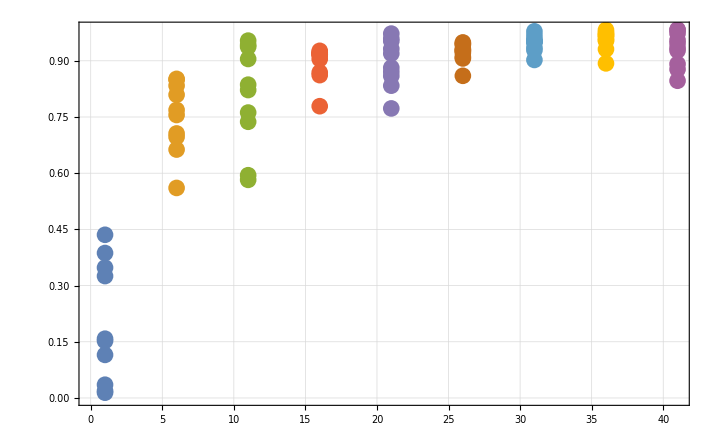

```mathematica
testfairness = Table[ {nsteps, NoiseSim[ ghz[4], .6, nsteps]}, {nsteps, 1,41,5},{nexp, 1,10}];
ListPlot[testfairness, PlotTheme->"Detailed"]
```

Here is the dependence on error.

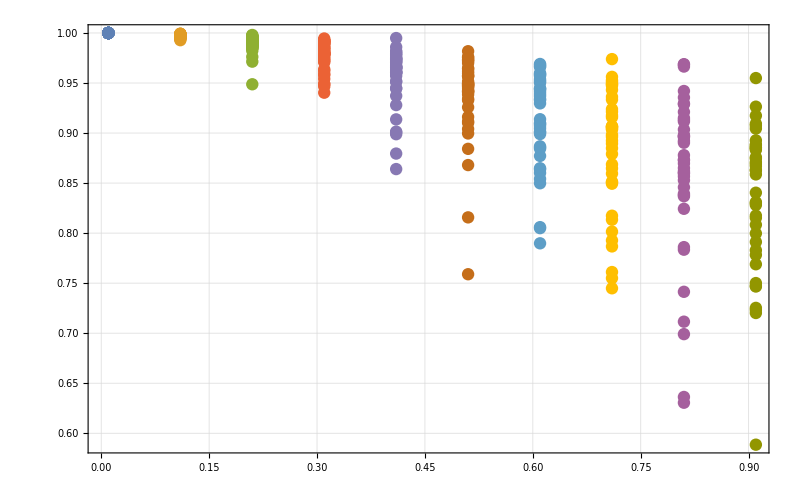

```mathematica
results = Table[ {err, NoiseSim[ ghz[4], err, 25]}, {err, .01,1,0.1},{nexp, 1,40}];
ListPlot[results, PlotTheme->"Detailed"]
```

For comparison, here is the behaviour for typical other states.

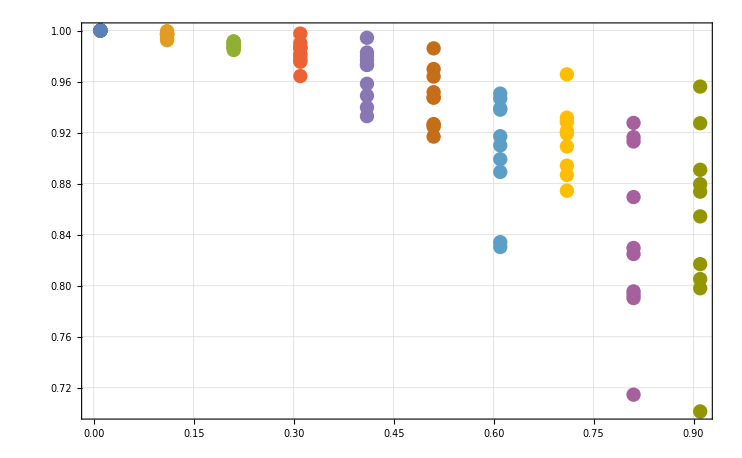

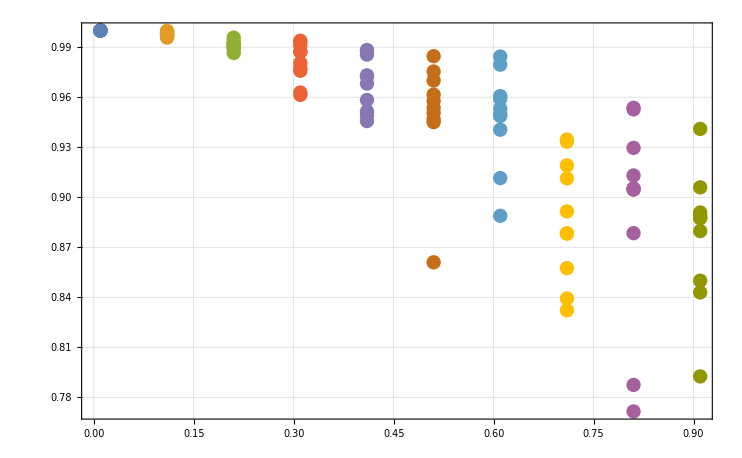

```mathematica
results2 = Table[ {err, NoiseSim[ Normalize[ RandomReal[1,2^4] ], err, 20]}, {err, .01,1,0.1},{nexp, 1,10}];
ListPlot[results2, PlotTheme->"Detailed"]
results3 = Table[ {err, NoiseSim[ Normalize[Table[1,{site,1,2^4}] ], err, 20]}, {err, .01,1,0.1},{nexp, 1,10}];
ListPlot[results3, PlotTheme->"Detailed"]
```

```mathematica
z
```

Conclusion: The GHZ state is not any more susceptible to errors than any other state.

## Testing with Measurement errors

Assume the first Qubit is accidentaly measured. What is the effect if we measure 0? What is the effect if we measure 1?

```mathematica
n=5;
measure1 = Table[ Sqrt[2] Boole[ i > 2^(n-1)], {i,1,2^n}];
measure0 = Table[ Sqrt[2] Boole[ i <= 2^(n-1)], {i,1,2^n}];
state1 = MatrixExp[ -I Hg[n] Pi/2 , uniform[n] ];

indexEvenNumbers[n_] := Boole[EvenQ[Total /@ IntegerDigits[Range[0,n-1],2] ]] (* Gives the index of vectors with EVEN partiy *)
probEven[vector_]:=  Abs[vector]^2 . indexEvenNumbers[Length[vector]]  (* Gives the probability of measureing EVEN parity on the given vector *)
```

### Effect on the g-pulse GHZ-state

```mathematica
output = {{"Question","No Measurement", "Measure 0","Measure 1"}};
singleUnitary[xi_]:= If[ EvenQ[xi], ConjugateTranspose[MatrixPower[Y,1/2]] ,ConjugateTranspose[MatrixPower[Z,1/2]]  ]; (* Gives Sqrt[Y] or Sqrt[Z] depending on question x_i = 0 or 1 *)
fullUnitary[ question_ ] := ( fullunitary = {1};  For[ i=1, i≤n, i++, fullunitary = KroneckerProduct[singleUnitary[question⟦i⟧ ], fullunitary] ]; fullunitary ) (* Makes the n-bit unitary for a question x *)

For[ j = 1,j≤ Length[ questions[n] ], j++,

x = questions[n]⟦j⟧;
probcorrect = probEven[ fullUnitary[x] . state1 ];
pcorrect0 = probEven[ fullUnitary[x] . (measure0 * state1) ];
pcorrect1 = probEven[ fullUnitary[x] . (measure1 * state1) ];

goal =Mod[Total[x]/2,2];
If[ EvenQ[goal] == False, 
(pcorrect0 = 1-pcorrect0; 
pcorrect1 = 1-pcorrect1;
probcorrect = 1-probcorrect;)
];

output = Append[ output, {x, probcorrect, pcorrect0, pcorrect1} ];
]

means =Mean[  output[[2;;, 2;;]] ] ;
output = Append[ output, Join[ {"Averages"}, means ] ];
Panel[ Style [ 
 Grid[ output, Background->{None,{{LightBlue,LightGray} }} , ItemSize-> All, Spacings -> {2,2} ] 
]
] // TraditionalForm
```

Question | No Measurement | Measure 0 | Measure 1
{0,0,0,0,0} | 1 | 1/2 | 1/2
{0,0,0,1,1} | 1 | 1 | 1
{0,0,1,0,1} | 1 | 1 | 1
{0,0,1,1,0} | 1 | 1/2 | 1/2
{0,1,0,0,1} | 1 | 1 | 1
{0,1,0,1,0} | 1 | 1/2 | 1/2
{0,1,1,0,0} | 1 | 1/2 | 1/2
{0,1,1,1,1} | 1 | 1 | 1
{1,0,0,0,1} | 1 | 1 | 1
{1,0,0,1,0} | 1 | 1/2 | 1/2
{1,0,1,0,0} | 1 | 1/2 | 1/2
{1,0,1,1,1} | 1 | 1 | 1
{1,1,0,0,0} | 1 | 1/2 | 1/2
{1,1,0,1,1} | 1 | 1 | 1
{1,1,1,0,1} | 1 | 1 | 1
{1,1,1,1,0} | 1 | 1/2 | 1/2
Averages | 1 | 3/4 | 3/4

```mathematica
Grid
```

### Effect on the normal GHZ-state

```mathematica
output = {{"Question","No Measurement", "Measure 0","Measure 1"}};
singleUnitary[xi_]:= If[ EvenQ[xi], H ,H.MatrixPower[Z,1/2]  ]; 
fullUnitary[ question_ ] := ( fullunitary = {1};  For[ i=1, i≤n, i++, fullunitary = KroneckerProduct[singleUnitary[question⟦i⟧ ], fullunitary] ]; fullunitary ) (* Makes the n-bit unitary for a question x *)

For[ j = 1,j≤ Length[ questions[n] ], j++,

x = questions[n]⟦j⟧;
probcorrect = probEven[ fullUnitary[x] . ghz[n] ];
pcorrect0 = probEven[ fullUnitary[x] . (measure0 * state1) ];
pcorrect1 = probEven[ fullUnitary[x] . (measure1 * state1) ];

goal =Mod[Total[x]/2,2];
If[ EvenQ[goal] == False, 
(pcorrect0 = 1-pcorrect0; 
pcorrect1 = 1-pcorrect1;
probcorrect = 1-probcorrect;)
];

output = Append[ output, {x, probcorrect, pcorrect0, pcorrect1} ];
]

means =Mean[  output[[2;;, 2;;]] ] ;
output = Append[ output, Join[ {"Averages"}, means ] ];

Panel[ Style [ 
 Grid[ output, Background->{None,{{LightBlue,LightGray} }} , ItemSize->All] , 
FontFamily-> "Calibri", 14]
]
```

Question | No Measurement | Measure 0 | Measure 1
{0,0,0,0,0} | 1 | 1/2 | 1/2
{0,0,0,1,1} | 1 | 1/2 | 1/2
{0,0,1,0,1} | 1 | 1/2 | 1/2
{0,0,1,1,0} | 1 | 1/2 | 1/2
{0,1,0,0,1} | 1 | 1/2 | 1/2
{0,1,0,1,0} | 1 | 1/2 | 1/2
{0,1,1,0,0} | 1 | 1/2 | 1/2
{0,1,1,1,1} | 1 | 1/2 | 1/2
{1,0,0,0,1} | 1 | 1/2 | 1/2
{1,0,0,1,0} | 1 | 1/2 | 1/2
{1,0,1,0,0} | 1 | 1/2 | 1/2
{1,0,1,1,1} | 1 | 1/2 | 1/2
{1,1,0,0,0} | 1 | 1/2 | 1/2
{1,1,0,1,1} | 1 | 1/2 | 1/2
{1,1,1,0,1} | 1 | 1/2 | 1/2
{1,1,1,1,0} | 1 | 1/2 | 1/2
Averages | 1 | 1/2 | 1/2

## Messing around - Can we “cut” the large GHZ-state into smaller pieces? (e.g. free up an ancilla in the middle?)

```mathematica
ghz[5]
```

{1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2)}

```mathematica
ghz[3]
```

{1/(√2),0,0,0,0,0,0,1/(√2)}

```mathematica
sx = MatrixPower[X,1/2]
```

{{1/2+ⅈ/2,1/2-ⅈ/2},{1/2-ⅈ/2,1/2+ⅈ/2}}

```mathematica
sx3 = KroneckerProduct[sx,sx,sx]
```

{{-1/4+ⅈ/4,1/4+ⅈ/4,1/4+ⅈ/4,1/4-ⅈ/4,1/4+ⅈ/4,1/4-ⅈ/4,1/4-ⅈ/4,-1/4-ⅈ/4},{1/4+ⅈ/4,-1/4+ⅈ/4,1/4-ⅈ/4,1/4+ⅈ/4,1/4-ⅈ/4,1/4+ⅈ/4,-1/4-ⅈ/4,1/4-ⅈ/4},{1/4+ⅈ/4,1/4-ⅈ/4,-1/4+ⅈ/4,1/4+ⅈ/4,1/4-ⅈ/4,-1/4-ⅈ/4,1/4+ⅈ/4,1/4-ⅈ/4},{1/4-ⅈ/4,1/4+ⅈ/4,1/4+ⅈ/4,-1/4+ⅈ/4,-1/4-ⅈ/4,1/4-ⅈ/4,1/4-ⅈ/4,1/4+ⅈ/4},{1/4+ⅈ/4,1/4-ⅈ/4,1/4-ⅈ/4,-1/4-ⅈ/4,-1/4+ⅈ/4,1/4+ⅈ/4,1/4+ⅈ/4,1/4-ⅈ/4},{1/4-ⅈ/4,1/4+ⅈ/4,-1/4-ⅈ/4,1/4-ⅈ/4,1/4+ⅈ/4,-1/4+ⅈ/4,1/4-ⅈ/4,1/4+ⅈ/4},{1/4-ⅈ/4,-1/4-ⅈ/4,1/4+ⅈ/4,1/4-ⅈ/4,1/4+ⅈ/4,1/4-ⅈ/4,-1/4+ⅈ/4,1/4+ⅈ/4},{-1/4-ⅈ/4,1/4-ⅈ/4,1/4-ⅈ/4,1/4+ⅈ/4,1/4-ⅈ/4,1/4+ⅈ/4,1/4+ⅈ/4,-1/4+ⅈ/4}}

```mathematica
sx3.ghz[3]
```

{-1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2)}

```mathematica
sx5 = KroneckerProduct[sx,sx,sx3];
```

```mathematica
sx5.ghz[5]
```

{-1/(4 √2),-1/(4 √2),-1/(4 √2),1/(4 √2),-1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),-1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),-1/(4 √2),-1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),-1/(4 √2),1/(4 √2),1/(4 √2),1/(4 √2),-1/(4 √2),1/(4 √2),-1/(4 √2),-1/(4 √2),-1/(4 √2)}

```mathematica
sx4 = KroneckerProduct[sx3,sx];
```

```mathematica
sx4.ghz[4]
```

{-1/(2 √2),0,0,1/(2 √2),0,1/(2 √2),1/(2 √2),0,0,1/(2 √2),1/(2 √2),0,1/(2 √2),0,0,-1/(2 √2)}

```mathematica
KroneckerProduct[sx,sx].ghz[2]
```

{0,1/(√2),1/(√2),0}

```mathematica
h3 = KroneckerProduct[H,H,H]
```

{{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2)},{1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2)},{1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2)},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2)},{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2)},{1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2)},{1/(2 √2),1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2)},{1/(2 √2),-1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2)}}

```mathematica
h3.ghz[3]
```

{1/2,0,0,1/2,0,1/2,1/2,0}

```mathematica
h4 = KroneckerProduct[H,h3];
```